```mathematica
SetOptions[$FrontEnd,"ClearEvaluationQueueOnKernelQuit"->False];Quit[];
```

# MULTI-HIGGS HEFT FEYNCALC

```mathematica
$LoadAddOns={"FeynArts"};
Get["FeynCalc`"]
$FAVerbose = 0;
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"LOLagr"}]];
```

Successfully patched FeynArts.

```mathematica
SetOptions[FourVector, FeynCalcInternal->False];
```

```mathematica
Model["EWET.fr"];
```

## ww->3H

```mathematica
NoHiggsPotential=ExcludeFieldPoints->{FieldPoint[0][S[1],S[1],S[1]],FieldPoint[0][S[1],S[1],S[1],S[1]],FieldPoint[0][S[1],S[1],S[1],S[1],S[1]],FieldPoint[0][S[1],S[1],S[1],S[1],S[1],S[1]]};
```

```mathematica
diags=InsertFields[CreateTopologies[0,2->3,Adjacencies->{3,4,5,6}],{S[3],-S[3]}->{S[1],S[1],S[1]},ExcludeParticles-> {V[1],V[2],V[3]},Restrictions->{NoHiggsPotential},Model->FileNameJoin[{NotebookDirectory[],"LOLagr/LOLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"LOLagr/LOLagr"}],InsertionLevel->{Classes} ];
```

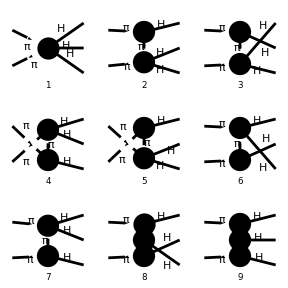

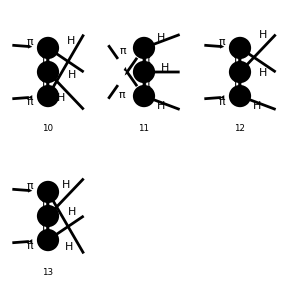

```mathematica
Paint[diags, ColumnsXRows -> {3, 3}, Numbering -> Simple,
	SheetHeader->None,AutoEdit->False];
```

```mathematica
prod[a_,b_]:=Pair[Momentum[a],Momentum[b]];
mas0={prod[p1,p1]->0,prod[p2,p2]->0,prod[k1,k1]->0,prod[k2,k2]->0,prod[k3,k3]->0,prod[k4,k4]->0};
consmom={p2->k1+k2+k3+k4-p1};
mandelstam={ prod[p1,k1]->s/2*f1*z1, prod[p1,k2]->s/2*f2*z2,prod[p1,k3]->s/2*f3*z3,prod[p1,k4]->s/2*f4*z4,prod[k1,k2]->s*f1*f2*z12,prod[k1,k3]->s*f1*f3*z13,prod[k1,k4]->s*f1*f4*z14,prod[k2,k3]->s*f2*f3*z23,prod[k2,k4]->s*f2*f4*z24,prod[k3,k4]->s*f3*f4*z34};
```

```mathematica
M=(ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},
	OutgoingMomenta->{k1,k2,k3,k4},List->True,ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]//PropagatorDenominatorExplicit]/.{c3u->a3,c4u->a4,vev->v}/.mas0/.consmom//ExpandScalarProduct)/.mas0
```

{-(6 a3 (OverBar[k1]·OverBar[p1]+OverBar[k2]·OverBar[p1]+OverBar[k3]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/v^3,-(4 a b (OverBar[k1]·OverBar[k2]+OverBar[k1]·OverBar[k3]+2 (OverBar[k2]·OverBar[k3])+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1]+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1]) (OverBar[k1]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/(v^3 (2 (OverBar[k2]·OverBar[k3])-2 (OverBar[k1]·OverBar[k2]+OverBar[k2]·OverBar[k3]+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1])-2 (OverBar[k1]·OverBar[k3]+OverBar[k2]·OverBar[k3]+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1]))),-(4 a b (OverBar[k1]·OverBar[k2]+2 (OverBar[k1]·OverBar[k3])+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1]+OverBar[k2]·OverBar[k3]+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1]) (OverBar[k2]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/(v^3 (2 (OverBar[k1]·OverBar[k3])-2 (OverBar[k1]·OverBar[k2]+OverBar[k1]·OverBar[k3]+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1])-2 (OverBar[k1]·OverBar[k3]+OverBar[k2]·OverBar[k3]+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1]))),-(4 a b (2 (OverBar[k1]·OverBar[k2])+OverBar[k1]·OverBar[k3]+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1]+OverBar[k2]·OverBar[k3]+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1]) (OverBar[k3]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/(v^3 (2 (OverBar[k1]·OverBar[k2])-2 (OverBar[k1]·OverBar[k2]+OverBar[k1]·OverBar[k3]+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1])-2 (OverBar[k1]·OverBar[k2]+OverBar[k2]·OverBar[k3]+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1]))),(2 a b (OverBar[k2]·OverBar[p1]+OverBar[k3]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/v^3,(2 a b (OverBar[k1]·OverBar[p1]+OverBar[k3]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/v^3,(2 a b (OverBar[k1]·OverBar[p1]+OverBar[k2]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/v^3,(4 a^3 (OverBar[k1]·OverBar[k3]+2 (OverBar[k1]·OverBar[k2]+OverBar[k2]·OverBar[k3]+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1])+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1]) (OverBar[k1]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/(v^3 (2 (OverBar[k2]·OverBar[k3])-2 (OverBar[k1]·OverBar[k2]+OverBar[k2]·OverBar[k3]+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1])-2 (OverBar[k1]·OverBar[k3]+OverBar[k2]·OverBar[k3]+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1]))),(4 a^3 (OverBar[k1]·OverBar[k2]+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1]+2 (OverBar[k1]·OverBar[k3]+OverBar[k2]·OverBar[k3]+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1])) (OverBar[k1]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/(v^3 (2 (OverBar[k2]·OverBar[k3])-2 (OverBar[k1]·OverBar[k2]+OverBar[k2]·OverBar[k3]+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1])-2 (OverBar[k1]·OverBar[k3]+OverBar[k2]·OverBar[k3]+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1]))),(4 a^3 (2 (OverBar[k1]·OverBar[k2]+OverBar[k1]·OverBar[k3]+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1])+OverBar[k2]·OverBar[k3]+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1]) (OverBar[k2]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/(v^3 (2 (OverBar[k1]·OverBar[k3])-2 (OverBar[k1]·OverBar[k2]+OverBar[k1]·OverBar[k3]+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1])-2 (OverBar[k1]·OverBar[k3]+OverBar[k2]·OverBar[k3]+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1]))),(4 a^3 (2 (OverBar[k1]·OverBar[k2]+OverBar[k1]·OverBar[k3]+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1])+OverBar[k2]·OverBar[k3]+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1]) (OverBar[k3]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/(v^3 (2 (OverBar[k1]·OverBar[k2])-2 (OverBar[k1]·OverBar[k2]+OverBar[k1]·OverBar[k3]+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1])-2 (OverBar[k1]·OverBar[k2]+OverBar[k2]·OverBar[k3]+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1]))),(4 a^3 (OverBar[k1]·OverBar[k2]+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1]+2 (OverBar[k1]·OverBar[k3]+OverBar[k2]·OverBar[k3]+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1])) (OverBar[k2]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/(v^3 (2 (OverBar[k1]·OverBar[k3])-2 (OverBar[k1]·OverBar[k2]+OverBar[k1]·OverBar[k3]+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1])-2 (OverBar[k1]·OverBar[k3]+OverBar[k2]·OverBar[k3]+OverBar[k3]·OverBar[k4]-OverBar[k3]·OverBar[p1]))),(4 a^3 (OverBar[k1]·OverBar[k3]+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1]+2 (OverBar[k1]·OverBar[k2]+OverBar[k2]·OverBar[k3]+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1])) (OverBar[k3]·OverBar[p1]+OverBar[k4]·OverBar[p1]))/(v^3 (2 (OverBar[k1]·OverBar[k2])-2 (OverBar[k1]·OverBar[k2]+OverBar[k1]·OverBar[k3]+OverBar[k1]·OverBar[k4]-OverBar[k1]·OverBar[p1])-2 (OverBar[k1]·OverBar[k2]+OverBar[k2]·OverBar[k3]+OverBar[k2]·OverBar[k4]-OverBar[k2]·OverBar[p1])))}

```mathematica
MMandel=Simplify[M/.mandelstam]
```

{-(3 a3 s (f1 z1+f2 z2+f3 z3+f4 z4))/v^3,(a b s (f1 z1+f4 z4) (2 f1 (f2 z12+f3 z13)+4 f2 f3 z23+2 f2 f4 z24-f2 z2+2 f3 f4 z34-f3 z3))/(v^3 (2 f1 (f2 z12+f3 z13)+2 f2 f3 z23+2 f2 f4 z24-f2 z2+2 f3 f4 z34-f3 z3)),(a b s (f2 z2+f4 z4) (f1 (z1-2 (f2 z12+2 f3 z13+f4 z14))+f3 (-2 f2 z23-2 f4 z34+z3)))/(v^3 (f1 (z1-2 (f2 z12+f3 z13+f4 z14))+f3 (-2 f2 z23-2 f4 z34+z3))),(a b s (f3 z3+f4 z4) (f1 (z1-2 (2 f2 z12+f3 z13+f4 z14))+f2 (z2-2 (f3 z23+f4 z24))))/(v^3 (f1 (z1-2 (f2 z12+f3 z13+f4 z14))+f2 (z2-2 (f3 z23+f4 z24)))),(a b s (f2 z2+f3 z3+f4 z4))/v^3,(a b s (f1 z1+f3 z3+f4 z4))/v^3,(a b s (f1 z1+f2 z2+f4 z4))/v^3,-(a^3 s (f1 z1+f4 z4) (4 f1 f2 z12+2 f1 f3 z13+4 f2 f3 z23+4 f2 f4 z24-2 f2 z2+2 f3 f4 z34-f3 z3))/(v^3 (2 f1 (f2 z12+f3 z13)+2 f2 f3 z23+2 f2 f4 z24-f2 z2+2 f3 f4 z34-f3 z3)),-(a^3 s (f1 z1+f4 z4) (2 f1 f2 z12+4 f1 f3 z13+4 f2 f3 z23+2 f2 f4 z24-f2 z2+4 f3 f4 z34-2 f3 z3))/(v^3 (2 f1 (f2 z12+f3 z13)+2 f2 f3 z23+2 f2 f4 z24-f2 z2+2 f3 f4 z34-f3 z3)),-(a^3 s (f2 z2+f4 z4) (2 f1 (z1-2 (f2 z12+f3 z13+f4 z14))+f3 (-2 f2 z23-2 f4 z34+z3)))/(v^3 (f1 (z1-2 (f2 z12+f3 z13+f4 z14))+f3 (-2 f2 z23-2 f4 z34+z3))),-(a^3 s (f3 z3+f4 z4) (2 f1 (z1-2 (f2 z12+f3 z13+f4 z14))+f2 (z2-2 (f3 z23+f4 z24))))/(v^3 (f1 (z1-2 (f2 z12+f3 z13+f4 z14))+f2 (z2-2 (f3 z23+f4 z24)))),-(a^3 s (f2 z2+f4 z4) (f1 (z1-2 (f2 z12+2 f3 z13+f4 z14))+2 f3 (-2 f2 z23-2 f4 z34+z3)))/(v^3 (f1 (z1-2 (f2 z12+f3 z13+f4 z14))+f3 (-2 f2 z23-2 f4 z34+z3))),-(a^3 s (f3 z3+f4 z4) (f1 (z1-2 (2 f2 z12+f3 z13+f4 z14))+2 f2 (z2-2 (f3 z23+f4 z24))))/(v^3 (f1 (z1-2 (f2 z12+f3 z13+f4 z14))+f2 (z2-2 (f3 z23+f4 z24))))}

## ww->4H

```mathematica
NoHiggsPotential=ExcludeFieldPoints->{FieldPoint[0][S[1],S[1],S[1]],FieldPoint[0][S[1],S[1],S[1],S[1]],FieldPoint[0][S[1],S[1],S[1],S[1],S[1]],FieldPoint[0][S[1],S[1],S[1],S[1],S[1],S[1]]};
```

```mathematica
diags=InsertFields[CreateTopologies[0,2->4,Adjacencies->{3,4,5,6}],{S[3],-S[3]}->{S[1],S[1],S[1],S[1]},ExcludeParticles-> {V[1],V[2],V[3]},Restrictions->{NoHiggsPotential},Model->FileNameJoin[{NotebookDirectory[],"LOLagr/LOLagr"}],GenericModel->FileNameJoin[{NotebookDirectory[],"LOLagr/LOLagr"}],InsertionLevel->{Classes} ];
```

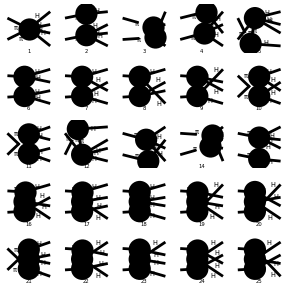

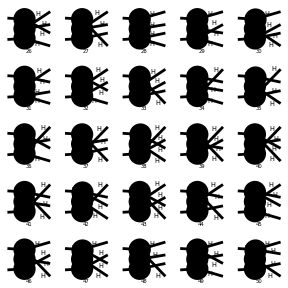

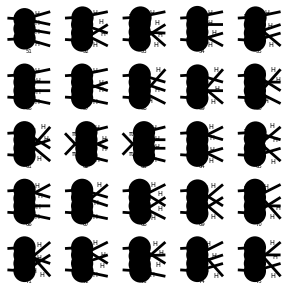

```mathematica
Paint[diags, ColumnsXRows -> {5, 5}, Numbering -> Simple,
	SheetHeader->None,AutoEdit->False];
```

```mathematica
prod[a_,b_]:=Pair[Momentum[a],Momentum[b]];
mas0={prod[p1,p1]->0,prod[p2,p2]->0,prod[k1,k1]->0,prod[k2,k2]->0,prod[k3,k3]->0,prod[k4,k4]->0};
consmom={p2->k1+k2+k3+k4-p1};
mandelstam={ prod[p1,k1]->s/2*f1*z1, prod[p1,k2]->s/2*f2*z2,prod[p1,k3]->s/2*f3*z3,prod[p1,k4]->s/2*f4*z4,prod[k1,k2]->s*f1*f2*z12,prod[k1,k3]->s*f1*f3*z13,prod[k1,k4]->s*f1*f4*z14,prod[k2,k3]->s*f2*f3*z23,prod[k2,k4]->s*f2*f4*z24,prod[k3,k4]->s*f3*f4*z34};
```

```mathematica
M=(ExpandScalarProduct[FCFAConvert[CreateFeynAmp[diags],IncomingMomenta->{p1,p2},
	OutgoingMomenta->{k1,k2,k3,k4},List->True,ChangeDimension->4,DropSumOver->True,SMP->True,Contract->True]//PropagatorDenominatorExplicit]/.{c3u->a3,c4u->a4,vev->v}/.mas0/.consmom//ExpandScalarProduct)/.mas0
```

```mathematica
MMandel=M/.mandelstam
```